```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\samfl\Documents\03_Kurser\KTH-Mathematica\Statistics

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
?randomExample
```

randomExample[n] gives n randomnumbers from a secret distribution.

```mathematica
ClearAll["`*"]
```

```mathematica
n=10000;
𝕩=randomNumber[4, n];
Short[𝕩];
𝕩sort=Sort[𝕩];
```

```mathematica
Δ=1/n;
```

```mathematica
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
Short[𝕡data];
```

```mathematica
𝕩𝕡data=Transpose[{𝕩sort,𝕡data}];
```

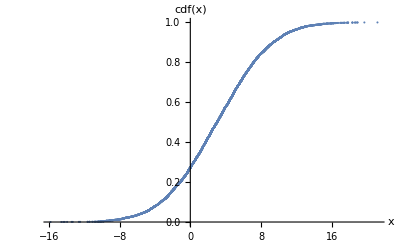

```mathematica
ListPlot[𝕩𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

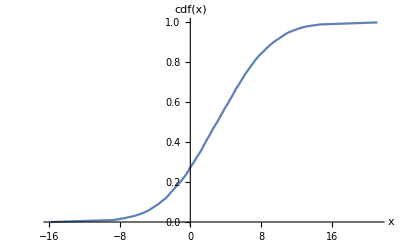

```mathematica
qdata=Table[{Quantile[𝕩,q],q},{q,0,1,0.01}];
ListLinePlot[qdata,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

```mathematica
x=Mean[𝕩]
```

3.0208

```mathematica
s=StandardDeviation[𝕩]
```

4.96161

```mathematica
𝒩=NormalDistribution[x,s]
```

NormalDistribution[3.0208,4.96161]

```mathematica
𝕡model=CDF[𝒩,𝕩sort];
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

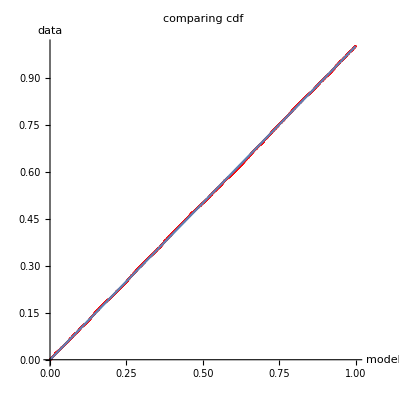

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

```mathematica
Clear[α,β];
```

```mathematica
𝒢=EstimatedDistribution[𝕩,NormalDistribution[α,β]]
```

NormalDistribution[3.0208,4.96136]

```mathematica
𝕡model=CDF[𝒢,𝕩sort];
𝕩sort;
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

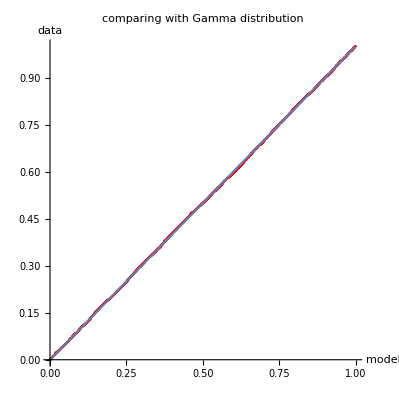

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```